```mathematica
u090494e　荒井直幸　2015年1月13日
```

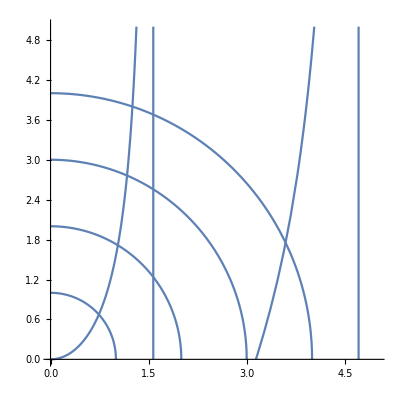

```mathematica
graph1=Plot[x Tan[x],{x,0,5},PlotRange->{0,5},AspectRatio->1];
Table[G[n]=Plot[Sqrt[n^2-x^2],{x,0,n},AspectRatio->1],{n,4}];
Show[graph1,G[1],G[2],G[3],G[4]]
```

0.739085

0.673612

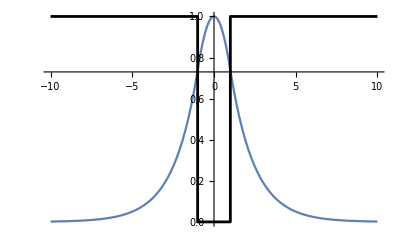

```mathematica
FindRoot[{Sqrt[1^2-x^2]==x Tan[x]},{x,0.5}];
k1=x/.%
k2=k1*Tan[k1]
graph2=Plot[Cos[k1 x],{x,-1,1},PlotRange->All];
c=Exp[k2] Cos[k1];
graph3=Plot[c Exp[-k2 x],{x,1,10},PlotRange->All];
graph4=Plot[c Exp[k2 x],{x,-10,-1},PlotRange->All];
graph5=Graphics[{AbsoluteThickness[2],Line[{{-10,1},{-1,1},{-1,0},{1,0},{1,1},{10,1}}]}];
Show[graph2,graph3,graph4,graph5]
```

```mathematica
課題１
```

3.5953

1.75322

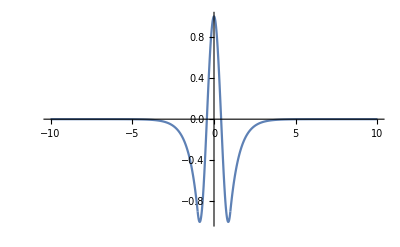

```mathematica
FindRoot[{Sqrt[4^2-x^2]==x Tan[x]},{x,0.5}];
k3=x/.%
k4=k3*Tan[k3]
graph6=Plot[Cos[k3 x],{x,-1,1},PlotRange->All];
c=Exp[k4] Cos[k3];
graph7=Plot[c Exp[-k4 x],{x,1,10},PlotRange->All];
graph8=Plot[c Exp[k4 x],{x,-10,-1},PlotRange->All];
Show[graph6,graph7,graph8]
```

```mathematica
課題２
```

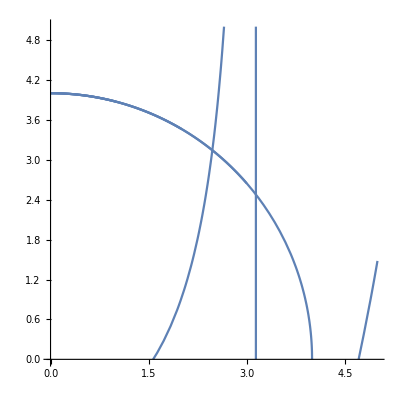

```mathematica
graph9=Plot[-x/Tan[x],{x,0,5},PlotRange->{0,5},AspectRatio->1];
Table[H[n]=Plot[Sqrt[4^2-x^2],{x,0,n},AspectRatio->1],{n,4}];
Show[graph9,H[1],H[2],H[3],H[4]]
```